## Making data

### Control Case: Randomly choose rule

```mathematica
Clear["Global`*"]
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
(*Sets up nice computer memry partitions*)

(*setsup the rule table in a way the code can use*)
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

(*set up initial parameters*)
width=3;
timesteps=2^width;
ics=Tuples[{0,1},width];
(*CHANGE HERE*) rules={15,27,29,39,43,45,51,53,57,71,75,77,83,85,89,99,101,113,142,154,156,166,170,172,178,180,184,198,202,204,210,212,216,226,228,240};

(*Now it's going to do a loop within a loop. It loops over all reversible rules and then it loops over all possible initial conditions*)
data=
Table[
Table[

oic=ics[[i]];
orule=rules[[k]];
orule=rule;

(*****organism setup*****)
state=oic;
initialstate=state;

(******Check to change rule at every time step******)
(*Organism before the mutation*)
ruleone=rule;
stateone=state;

smallsteps=Table[
(*Take the current environment state and the current organism state and compare them in an arbitrary way*)
(*Take the output of that arbitrary comparison and determine one of the six rules from it: JK PICK A RANDOM RULE INSTEAD*)
(*Apply that new rule to the current organism state*)
(*rename the new organism state to stateone*)
(*rename the new rule of the organism to ruleone*)
(*Put these replacements in the rule, making a new rule.*)
(*CHANGE HERE*) newrule1=RandomChoice[{15,27,29,39,43,45,51,53,57,71,75,77,83,85,89,99,101,113,142,154,156,166,170,172,178,180,184,198,202,204,210,212,216,226,228,240}];
newrule=ruletable[[newrule1+1]];
(*Apply the rule to the state*)
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;
(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,Flatten[Position[ruletable,rule]-1]}
,{j,1,timesteps}];
(*Has a weird output*)

CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
{CAorganism,organismrules}

,{k,1,Length[rules]}]
,{i,1,Length[ics]}];


(*Save the data to a file*)
Export["RandomRules_width"<>ToString[width]<>".csv",data]
```

RandomRules_width3.csv

### Classic Case: Env -> Org (where env is the same size as the organism)

```mathematica
(*Sets up nice computer memory partitions*)
Clear["Global`*"]
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
(*setsup the rule table in a way the code can use*)
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];
(*set up initial parameters*)
width=3;
timesteps=2*2^width;
ics=Tuples[{0,1},width];


(*!!!!!!!!!CHANGE HERE!!!!!!!!!*) rules={15,27,29,39,43,45,51,53,57,71,75,77,83,85,89,99,101,113,142,154,156,166,170,172,178,180,184,198,202,204,210,212,216,226,228,240};


(*First, our initial conditions are something like <envinronment initial cond, environment rule, organism init cond, organism rule>. So we gotta set those up*)

(*Well for width 3, that gives is 80K possible initial conditions. XD So let's just randomly pick 1000 for now*)
worldics = RandomSample[Tuples[{ics,rules,ics,rules}],width*1000];


(*Okies, now we do a loops over all our world initial conditions!*)
data=
Table[

eic = worldics[[i]][[1]];
erule = worldics[[i]][[2]];
oic=worldics[[i]][[3]]; 
orule=worldics[[i]][[4]];

(*set up the organism*)
state=oic;
rule=orule;
(*set up the environment*)
environment = CellularAutomaton[erule,eic,timesteps];

smallsteps=
Table[
number=width*Total[state]+width*Total[environment[[j]]]+rule;
If[number>255,
newnumber=number-255,
newnumber = number];
newrule=Nearest[rules,newnumber][[1]];
newrule1=ruletable[[newrule+1]];
(*Apply that new rule to the current organism state*)
step=Nest[Partition[#,3,1,2]/.newrule1&,state,1];
(*rename the new organism state to 'state'*)
state=step;
(*rename the new rule of the organism to 'rule'*)
rule=newrule;

(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,environment[[j]],Flatten[Position[ruletable,newrule1]-1]}

(*Do this for the specified number of timesteps*)
,{j,1,timesteps}];



(*Makes the table's output prettier*)
f[x_]:=x[[2]];
environment=f/@smallsteps;
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
{environment,CAorganism,organismrules}

,{i,1,Length[worldics]}];

Export["Case2_Width"<>ToString[width]<>".csv",data]
```

Case2_Width3.csv

### New Case: Org <-> Org

```mathematica
Clear["Global`*"]
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
(*Sets up nice computer memry partitions*)

(*setsup the rule table in a way the code can use*)
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

(*set up initial parameters*)
width=3;
timesteps=2^width;
ics=Tuples[{0,1},width];
(*CHANGE HERE*) rules={15,27,29,39,43,45,51,53,57,71,75,77,83,85,89,99,101,113,142,154,156,166,170,172,178,180,184,198,202,204,210,212,216,226,228,240};

(*Now it's going to do a loop within a loop. It loops over all reversible rules and then it loops over all possible initial conditions*)
data=
Table[
Table[

oic=ics[[i]];
orule=rules[[k]];
orule=rule;

(*****organism setup*****)
state=oic;
initialstate=state;

(******Check to change rule at every time step******)
(*Organism before the mutation*)
ruleone=rule;
stateone=state;

smallsteps=Table[
(*Take the current environment state and the current organism state and compare them in an arbitrary way*)
(*Take the output of that arbitrary comparison and determine one of the six rules from it: JK PICK A RANDOM RULE INSTEAD*)
(*Apply that new rule to the current organism state*)
(*rename the new organism state to stateone*)
(*rename the new rule of the organism to ruleone*)
(*Put these replacements in the rule, making a new rule.*)
(*CHANGE HERE*) newrule1=RandomChoice[{15,27,29,39,43,45,51,53,57,71,75,77,83,85,89,99,101,113,142,154,156,166,170,172,178,180,184,198,202,204,210,212,216,226,228,240}];
newrule=ruletable[[newrule1+1]];
(*Apply the rule to the state*)
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;
(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,Flatten[Position[ruletable,rule]-1]}
,{j,1,timesteps}];
(*Has a weird output*)

CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps//Flatten;
{CAorganism,organismrules}

,{k,1,Length[rules]}]
,{i,1,Length[ics]}];


(*Save the data to a file*)
Export["RandomRules_width"<>ToString[width]<>".csv",data]
```

RandomRules_width3.csv

## Going through the data (run these code cells for each width :D)

### Initial Plots

```mathematica
width=3;
data=Import["Case2_Width"<>ToString[width]<>".csv"]//ToExpression;
ics=Tuples[{0,1},width];
possibletrajectories=Flatten[Table[Table[CellularAutomaton[i,ics[[j]],2*2^width-1],{i,0,255}],{j,1,Length[ics]}],1];
```

```mathematica
results=Table[
inno=If[
MemberQ[possibletrajectories,data[[i]][[2]]]==True,1,0];
info=
If[MemberQ[{ConstantArray[1,width],ConstantArray[0,width]},data[[i]][[2]][[1]]]==False,
1,0];
b={data[[i]][[2]],data[[i]][[3]]}//Transpose;
c=Table[Count[b[[1;;i]],b[[i]]],{i,1,Length[b]}];
d=Split[c];
If[Length[d]==1,
rt = "+";
att="NA";
oee1=1;
oee2="NA";
oee3=If[inno==1&&info==0,1,0];
oee4 = If[inno==0&&info==1,1,0];
,
rt = Length[d[[1]]];
att=Length/@d[[2;;Length[d]]]//Mean//Round;
oee1=If[inno==1&&info==1&&rt>2^width,1,0];
oee2=If[inno==1&&info==1&&rt>2^width&&att>2^width,1,0];
oee3=If[inno==1&&info==0&&rt>2^width,1,0];
oee4 = If[inno==0&&info==1&&rt>2^width,1,0];
];
{inno,info,rt,att,oee1,oee2,oee3,oee4}
,{i,1,Length[data]}];
```

RESULTS KEY: {innovative in states?, information-containing?, recurrence time, attractor size, is it oee?, is it oee in attractor too?, is it oee with no information?, oee without innovation?}
			1				2			3	       4		5		6				7				8
We are looking for OEE regardless of innovative states

```mathematica
OEEPercent =(((Last/@results)//Total)/Length[results]//N)100
```

26.7667

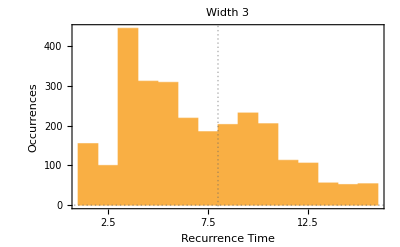

RT_Width3.pdf

```mathematica
f[x_]:=x[[3]]
plot=Histogram[DeleteCases[f/@results,"+"],PlotLabel->"Width "<>ToString[width],PlotTheme->"Business",FrameLabel->{"Recurrence Time","Occurences"},GridLines->{{2^width}, {0}}]
Export["RT_Width"<>ToString[width]<>".pdf",plot]
```

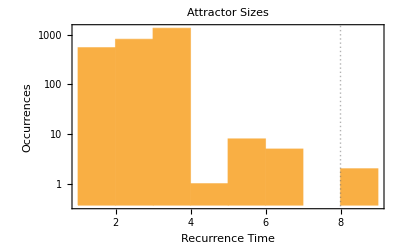

Att_Width3.pdf

```mathematica
f[x_]:=x[[4]]
Histogram[DeleteCases[f/@results,"NA"],PlotLabel->"Width "<>ToString[width],ScalingFunctions->"Log",PlotTheme->"Business",FrameLabel->{"Attractor Size","Occurrences"},GridLines->{{2^width}, {0}}]
Export["Att_Width"<>ToString[width]<>".pdf",plot]
```

### But what do they meaaaannnn

## Ignore for now

### Make Histograms

```mathematica
Table[
width=m;
data = Import["RandomRules_width"<>ToString[width]<>".csv"]//ToExpression;
data2=Table[
Table[
a=data[[j]][[i]][[1]];
b=data[[j]][[i]][[2]];

If[MemberQ[a,ConstantArray[0,width]]||MemberQ[a,ConstantArray[1,width]],
whereitstops=DeleteCases[{Position[a,ConstantArray[0,width]][[1]],Position[a,ConstantArray[1,width]][[1]]},{}⟦1⟧]//Flatten//Min;
trajectory=a[[1;;whereitstops]];
ruletrajectory=b[[1;;whereitstops]],
trajectory=a;
ruletrajectory=b];

{trajectory//Length,ruletrajectory}
,{i,1,Length[data[[j]]]}],
{j,1,Length[data]}];
data3=
Flatten/@(Reverse/@Flatten[
Table[
Table[
Table[{data2[[k]][[j]][[1]],data2[[k]][[j]][[2]][[i]]},{i,1,Length[data2[[k]][[j]][[2]]]}]
,{j,1,Length[data2[[k]]]}]
,{k,1,Length[data2]}]
,2]//Tally);

(* LabelingFunction->(Placed[#[[1]],Above]&), *)
BubbleChart[data3,PlotLabel->"Width = "<>ToString[width],FrameLabel->{"Rule","Trajectory Length"},BubbleSizes->{0.01,0.1},LabelingFunction->(Placed[#[[1]],Tooltip]&),PlotTheme->"Business",AspectRatio->1/2,ImageSize->Medium]
,{m,3,7}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

These are plots that show how rules are related to trajectory length
Problem is, that trajectory length is totally decided by the initial conditions here: All information encoded in the IC is retained over time since these rules are reversable.
Most trajectories are going to be full length
Trajectories depend on ICs, not rules since information is preserved

### Older code bits!

```mathematica
Clear["Global`*"]
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
(*Sets up nice computer memry partitions*)
```

#### This is the stuff you can set to change the initial conditions

```mathematica
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

(*Set the initial conditions*)
width=3;
oic=RandomChoice[{0,1},width];
orule=RandomChoice[{15,51,85,170,204,240}];
ics={eic,oic,erule,orule}
```

{eic,{0,0,0},erule,51}

#### All this stuff is based on your initial conditions

```mathematica
(*Just ignore this*)
(*maxcompression=Table[
g[x_]:=IntegerDigits[x,2,w];
g/@RandomInteger[{0,2^w-1},2^width*2^w]//Compress//ByteCount
,{10000}]//Max;*)
```

```mathematica
(*defining more stuff, actually this is redundant*)
erule=ics[[3]];
orule=ics[[4]];
eIC=ics[[1]];
oIC=ics[[2]];
timesteps=200;
```

```mathematica
(*****environment setup*****)
environment=CellularAutomaton[erule,eIC,timesteps-1];
```

CellularAutomaton::nspecnl: Since rule specification erule is not a List, it must be an integer or a pure Boolean function.

```mathematica
(*****organism setup*****)
state=oIC;
initialstate=state;
```

```mathematica
(******Check to change rule at every time step******)
(*Organism before the mutation*)
ruleone=rule;
stateone=state;

smallsteps=Table[
(*Take the current environment state and the current organism state and compare them in an arbitrary way*)
(*Take the output of that arbitrary comparison and determine one of the six rules from it: JK PICK A RANDOM RULE INSTEAD*)
(*Apply that new rule to the current organism state*)
(*rename the new organism state to stateone*)
(*rename the new rule of the organism to ruleone*)
(*Put these replacements in the rule, making a new rule.*)
newrule1=RandomChoice[{15,51,85,170,204,240}];
newrule=ruletable[[newrule1+1]];
(*Apply the rule to the state*)
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;
(*OUTPUT of the table! will be the organism state and the organism rule*)
{state,Flatten[Position[ruletable,rule]-1]}
,{j,1,timesteps}];
(*Has a weird output*)
```

#### This is your output!

```mathematica
(******Raw Data*******)
CAorganism=First/@smallsteps;
organismrules=Last/@smallsteps;
Row[{Column[{"Environment",environment//ArrayPlot}],Column[{"Organism",CAorganism//ArrayPlot}]}]
```

ArrayPlot::mat: Argument CellularAutomaton[erule,eic,199] at position 1 is not a list of lists.

Environment
ArrayPlot[CellularAutomaton[erule,eic,199]]Organism
-Graphics-

```mathematica
(*(*Calculates the mutation rate*)
f[x_]:=x[[2]];
mutationrates=f/@smallsteps;
mutationpercent=(mutationrates/. 0->a /. _Integer->1 /. a ->0 //Total)/timesteps;*)
```

```mathematica
(*(*Compression*)
compression=(Compress[CAorganism]//ByteCount)/maxcompression//N;*)
```

```mathematica
(*(******Lyp Data*******)
timesteps=ics[[m]][[6]];
iniA=CAorganism[[1]];
iniB=ReplacePart[iniA,Ceiling[(width-1)/2]->Abs[iniA[[Ceiling[(width-1)/2]]]-1]];
Defects=ConstantArray[0,timesteps];
Defects[[1]]=Abs[iniA-iniB];

Do[
ruleDef=IntegerDigits[organismrules[[b]],2,8];
rule=MapThread[#->#2&,{Tuples[{1,0},3],ruleDef}];
StateAN=Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]/.rule;
Defects[[b+1]]=Total[Abs[(Abs[Map[ConstantArray[#,3]&,Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]]-ConstantArray[{{1,0,0},{0,1,0},{0,0,1}},width]]/.rule)-StateAN]*Partition[Append[Prepend[Defects[[b]],First@Defects[[b]]],Last@Defects[[b]]],3,1],{2}];
iniA=StateAN;
,{b,1,timesteps-1}];

lypdata=Transpose[{Range[1,timesteps],Map[Total,Defects]}];
model= Exp[k*t];
fit=FindFit[lypdata,model,k,t,WorkingPrecision->3];*)
```

### Which rules are reversable

```mathematica
(*set up initial parameters*)

Table[
width=k;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

DeleteCases[Table[
If[
(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)== 2^width,
rules[[i]]
]
,{i,1,Length[rules]}],Null]

,{k,3,8}]//Column
```

{15,27,29,39,43,45,51,53,57,71,75,77,83,85,89,99,101,113,142,154,156,166,170,172,178,180,184,198,202,204,210,212,216,226,228,240}
{15,51,85,105,150,170,204,240}
{15,45,51,75,85,89,101,105,150,154,166,170,180,204,210,240}
{15,51,85,170,204,240}
{15,45,51,75,85,89,101,105,150,154,166,170,180,204,210,240}
{15,51,85,105,150,170,204,240}

:3
Ok so plotting the rules wasn’t helpful at all
Plot state transition maps for trajectories
For each rule, what are on a common trajectory? Which trajectories match these rules, just for the reversable rule
Gonna have loops and things, what’s that list, unique trajectories that that rule has
Then measure how weird the trajectories are, something non-trivial about the rule transitions
Cut off trajectotores until all 0’s or all 1’s
Are there any rules over-represented in long trajectories? How often the rules change, the output was still consitent was the same rule, how often does the landscape changes, distance measure between rules
How often is a rule used as a function of trajectory
Trajectory length vs % sampled
All traejcoties of certain length, how many rule transitions, how many transitions were of a particular rule, so many times we would have seen that rule
Then see the correlation to state landscapes

Then compare to old experiemnts and how often there reversable rules were present in OEE cases
Maximize number of trajectores to get to different states

Doug: Doesn’t want to explore statement, drive to fixed point attractors to model regenerations, a small set
State and history dependent, map between states and rules, trying to minimize pattern changes but couldn’t find solutions for that
feed-forward (decision tree) looks ‘smoother’ than recurrent, recurrent breaks the smoothness (has backwards edges in the neural net)

Sara: 3 and 3, one is CG version of eachother, rule 60
Randomized topology for rule 150 or a CA (assume white cells on edge)
State dependent topology